```mathematica
Inbreeding figure for sigma=90 and sigma=75 and sigma=0
```

```mathematica
Quit[]
```

InputStream[…]

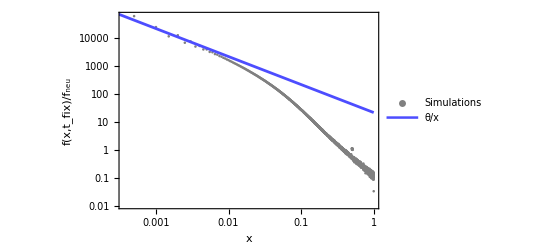

```mathematica
N1=1000;
mu=10^-6;
L=10000;
f=0.8181818181818181;
sa=(h + (1-h) f);
N1=N1/(1+f);
theta=4 N1 mu L; (* theta= 2 N mu *)
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/Inbreeeding_recombination/average_data_check_f.txt"]
datas1s=ReadList[s1s,{Number,Number}];

Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];


Data1s=Transpose@{x11s, x21s};

a1s=ListLogLogPlot[{Data1s}, Frame->True, FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003], FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Gray,Red,Magenta,Brown},PlotLegends->{"Simulations", "Diffusion"}];


a2s=LogLogPlot[ theta/( x),{x,10^-4,1},PlotStyle->{Lighter[Blue,0.3],Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\), \(x\)]\)",Medium]}];

a3s=LogLogPlot[theta/(2 1000 2 0.5 0.1 x^2),{x,0.1,1},PlotStyle->{Black,Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\\\ 
   \*SubscriptBox[\(p\), \(0\)]\), SuperscriptBox[\(x\), \(2\)]]\)",Medium]}];

Show[a1s,a2s]
```

```mathematica
(.9)/(2-.9)
```

0.818182

```mathematica
Quit[]
```

```mathematica
N1=1000;
mu=10^-6;
L=10000;
f=0.8181818181818181;
sa=(h + (1-h) f);
N1=N1/(1+f);
theta=4 N1 mu L; (* theta= 2 N mu *)
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/Inbreeeding_recombination/average_data_check_f.txt"]
datas1s=ReadList[s1s,{Number,Number}];

Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];


Data1s=Transpose@{x11s,  x21s};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium, FontSize->16],PlotStyle->{Black},PlotLegends->{"F = 0.818"},PlotRange->{{0.001,1},{0.003,40000}}, PlotMarkers->{"□",12}];

(*Show both plots*)
Show[a1sCombined]
```

InputStream[…]

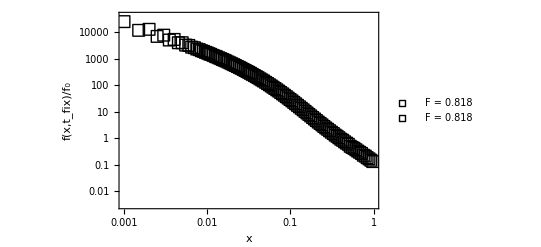

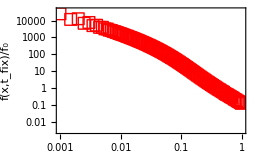
```mathematica
sig90=-Graphics-;
```

```mathematica
sigma=75 percent
```

```mathematica
Quit[]
```

```mathematica
N1=1000;
mu=10^-6;
L=10000;
f=0.6;
sa=(h + (1-h) f);
N1=N1/(1+f);
theta=4 N1 mu L; (* theta= 2 N mu *)
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/Inbreeeding_recombination/average_data_s_75_r_0_Ns_100.txt"]
datas1s=ReadList[s1s,{Number,Number}];

Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];


Data1s=Transpose@{x11s,  x21s};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium,FontSize->16],PlotStyle->{Blue},PlotLegends->{"F = 0.6"},PlotRange->{{0.001,1},{0.003,40000}}, PlotMarkers->{"△",10}];

(*Show both plots*)
Show[a1sCombined]
```

InputStream[…]

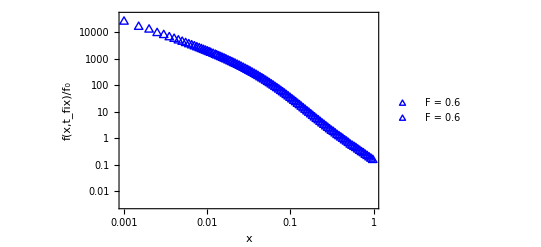

```mathematica
0.75/(2-0.75)
```

0.6

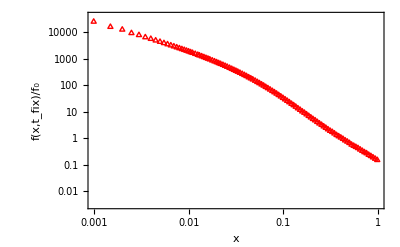
```mathematica
sig75=-Graphics-;
```

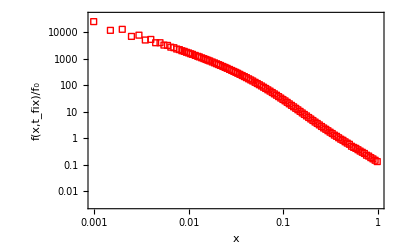
```mathematica
sig90=-Graphics-;
```

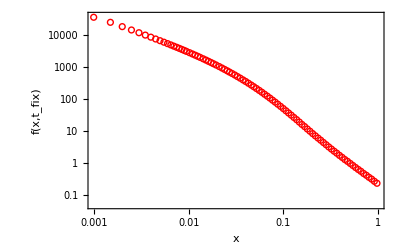
```mathematica
sig0=-Graphics-;
```

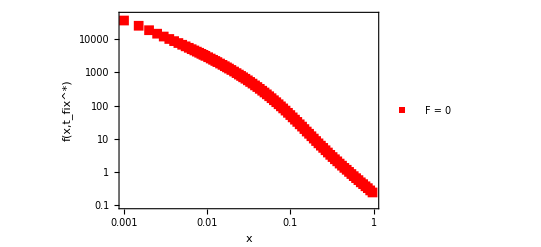
```mathematica
f0=-Graphics-;
```

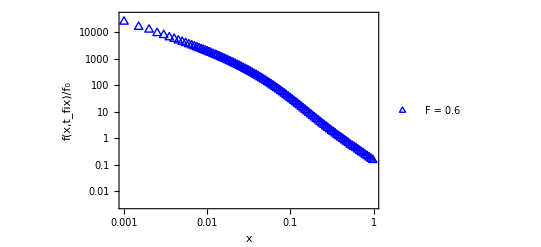
```mathematica
f6=-Graphics-;
```

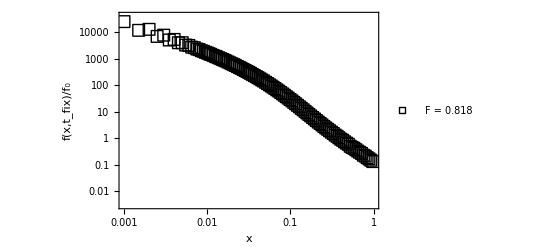
```mathematica
f818=-Graphics-;
```

```mathematica
Show[a1sCombined,f6,f818]
```

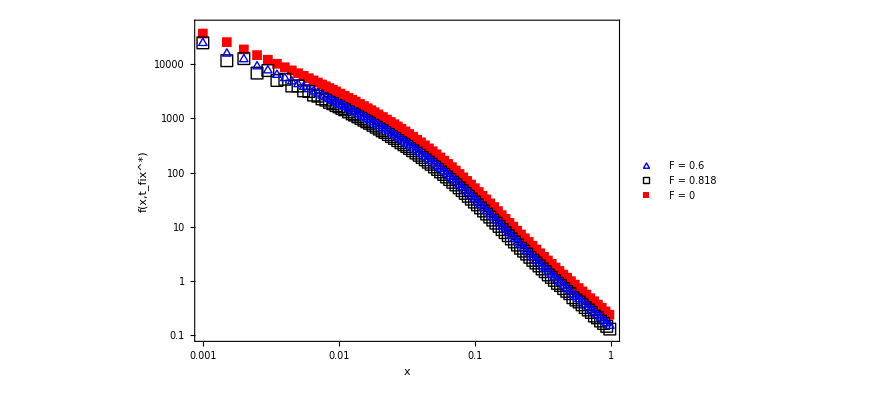

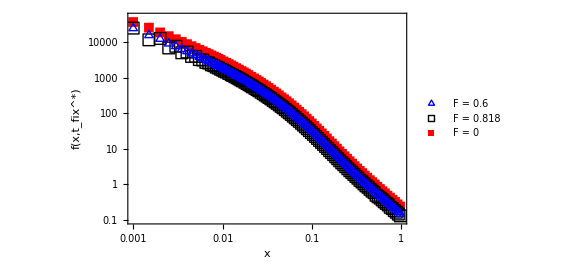

```mathematica
Show[sig0,sig75,sig90]
```

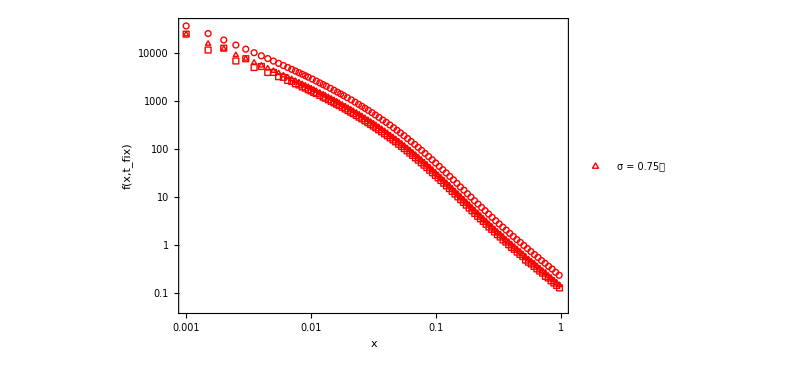

```mathematica
Quit[]
```

InputStream[…]

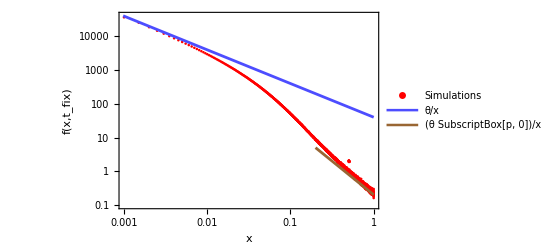

```mathematica
N1=1000;
mu=10^-7;
L=100000;
h=0.5;
sa=(h + (1-h) f);

theta=4 N1 mu L; (* theta= 2 N mu *)
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/hard_sweep/average_data_sweep_Ns_100.txt"]
datas1s=ReadList[s1s,{Number,Number}];

Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];


Data1s=Transpose@{x11s,x21s};

a1s=ListLogLogPlot[{Data1s}, Frame->True, FrameLabel->{"x","f(x,t_fix)"},FrameStyle->Thickness[.003], FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red,Magenta,Brown},PlotLegends->{"Simulations", "Diffusion"},PlotRange->{{ 0.001,1},{0.1,40000}}];


a2s=LogLogPlot[theta/(x),{x,0,1},PlotStyle->{Lighter[Blue,0.3],Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\), \(x\)]\)",Medium]}];

a3s=LogLogPlot[theta /(2 1000 2 0.5 0.1 x^2),{x,0.2,1},PlotStyle->{Brown,Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\\\ 
   \*SubscriptBox[\(p\), \(0\)]\), SuperscriptBox[\(x\), \(2\)]]\)",Medium]}];

Show[a1s,a2s,a3s]
```

```mathematica
Data1s=Transpose@{x11s, x21s};
(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.001;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Small],PlotStyle->{
Red},PlotLegends->{"σ = 0"},PlotRange->{{0.001,1},{0.05,40000}},PlotMarkers->{"○",10}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{Style["x",Italic],Style[Row[{Style["f(",Italic],Style["x",Italic],Style[",",Italic],SubsuperscriptBox[Style["t",Italic],Style["fix",Italic],"*"]//DisplayForm,Style[")",Italic]}]]},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium, FontSize->16],PlotStyle->{
Red},PlotLegends->{"F = 0 "},PlotRange->{{0.001,1},{0.1,5 10000}},PlotMarkers->{"■",10}];


(*Show both plots*)
Show[a1sCombined]
```

-Graphics-

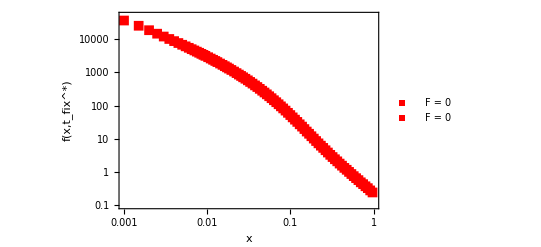

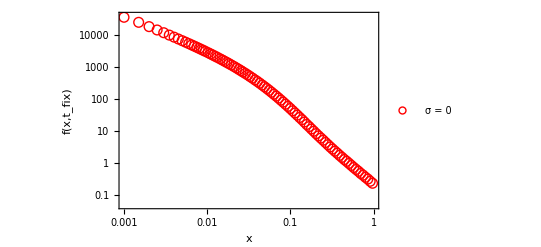

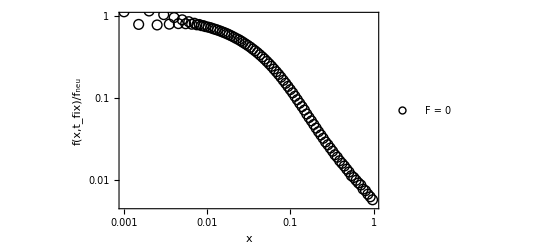

```mathematica
Data1s=Transpose@{x11s,x11s x21s/theta};
(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.001;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium, FontSize->12],PlotStyle->{
Black},PlotLegends->{"F = 0"},PlotRange->{{0.001,1},{0.005,1}},PlotMarkers->{"○",10}];
(*
a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium,FontSize->16],PlotStyle->{
RGBColor[0.77,0.14,0.]},PlotLegends->{"h=0.8"},PlotRange->{{0.001,1},{0.003,1}},PlotMarkers->{"\[MathematicaIcon]",8}]; *)

(*Show both plots*)
Show[a1sCombined]
```

```mathematica
Quit[]
```

InputStream[…]

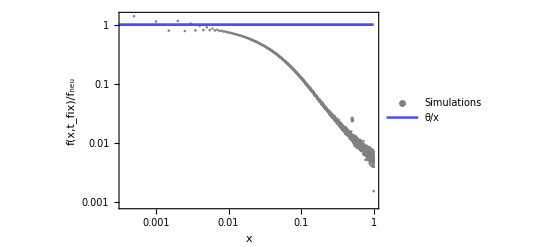

```mathematica
N1=1000;
mu=10^-6;
L=10000;
f=0.8181818181818181;
sa=(h + (1-h) f);
N1=N1/(1+f);
theta=4 N1 mu L; (* theta= 2 N mu *)
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/Inbreeeding_recombination/average_data_check_f.txt"]
datas1s=ReadList[s1s,{Number,Number}];

Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];


Data1s=Transpose@{x11s, x11s x21s/theta};

a1s=ListLogLogPlot[{Data1s}, Frame->True, FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003], FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Gray,Red,Magenta,Brown},PlotLegends->{"Simulations", "Diffusion"}];


a2s=LogLogPlot[x theta/(theta x),{x,10^-4,1},PlotStyle->{Lighter[Blue,0.3],Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\), \(x\)]\)",Medium]}];

a3s=LogLogPlot[theta/(2 1000 2 0.5 0.1 x^2),{x,0.1,1},PlotStyle->{Black,Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\\\ 
   \*SubscriptBox[\(p\), \(0\)]\), SuperscriptBox[\(x\), \(2\)]]\)",Medium]}];

Show[a1s,a2s]
```

```mathematica
(.75)/(2-.75)
```

0.6

InputStream[…]

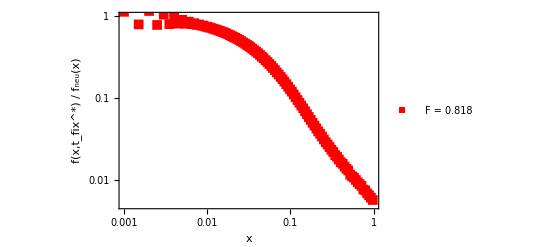

```mathematica
N1=1000;
mu=10^-6;
L=10000;
f=0.8181818181818181;
sa=(h + (1-h) f);
N1=N1/(1+f);
theta=4 N1 mu L; (* theta= 2 N mu *)
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/Inbreeeding_recombination/average_data_check_f.txt"]
datas1s=ReadList[s1s,{Number,Number}];

Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];


Data1s=Transpose@{x11s, x11s x21s/theta};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{
Red},PlotLegends->{"σ = 0.9 "},PlotRange->{{0.001,1},{0.005,1}},PlotMarkers->{"■",10}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{Style["x",Italic],Style[Row[{Style["f(",Italic],Style["x",Italic],Style[",",Italic],SubsuperscriptBox[Style["t",Italic],Style["fix",Italic],"*"]//DisplayForm,Style[") / ",Italic],SubscriptBox[Style["f",Italic],"neu"]//DisplayForm,Style["(x)",Italic]}]]},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium, FontSize->12],PlotStyle->{
Red},PlotLegends->{"F = 0.818 "},PlotRange->{{0.001,1},{0.005,1}},PlotMarkers->{"■",10}];


(*Show both plots*)
Show[a1sCombined]
```

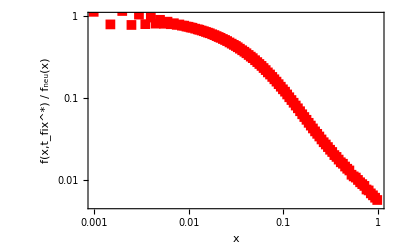
```mathematica
a1=-Graphics-;
```

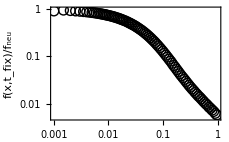
```mathematica
a2=-Graphics-;
```

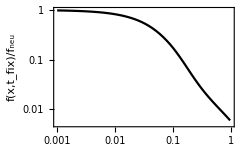
```mathematica
a3=-Graphics-;
```

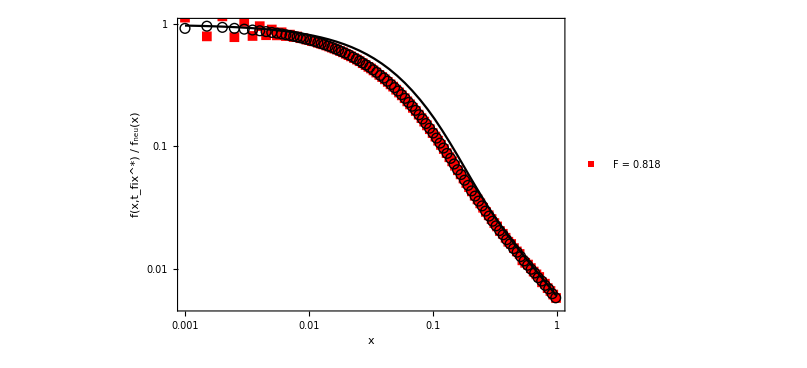

```mathematica
Show[a1sCombined,a2,a3]
```

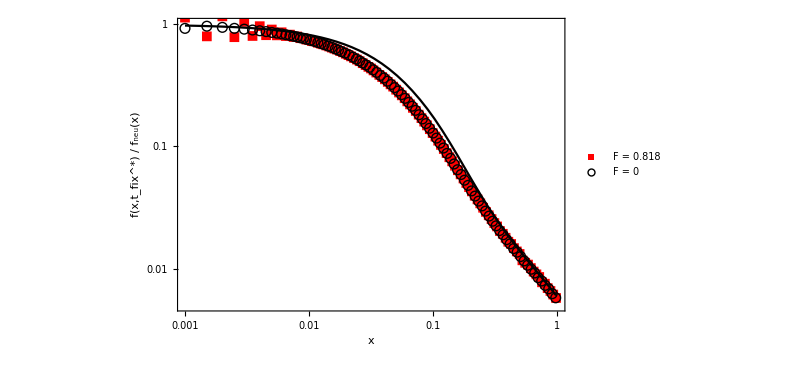

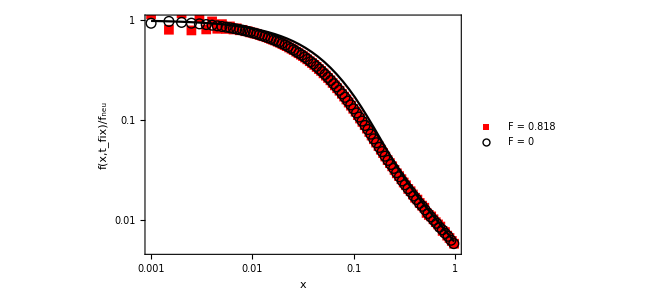

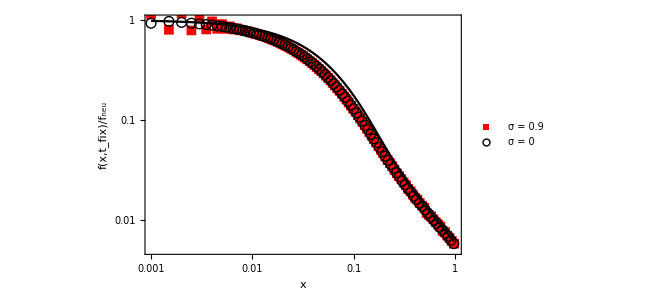

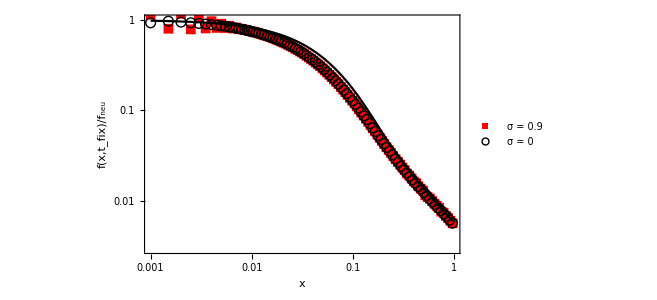

```mathematica
a2=-Graphics-;
```

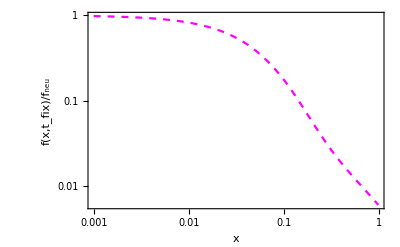
```mathematica
a3=-Graphics-;
```

```mathematica
Show[a1,a2,a3]
```

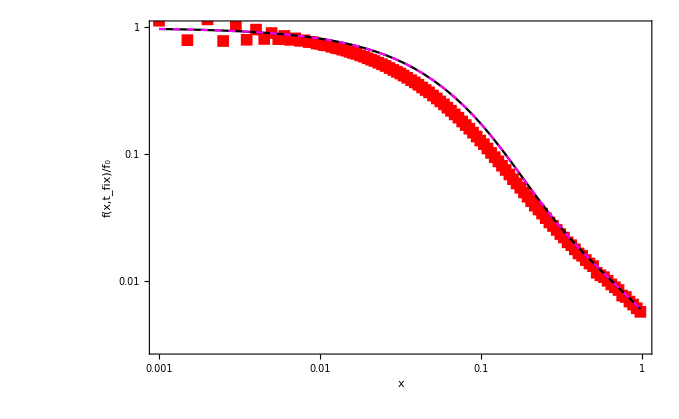
```mathematica
a1=-Graphics-;
```

```mathematica
a2=-Graphics-;
```

```mathematica
Show[a1,a2]
```

-Graphics-

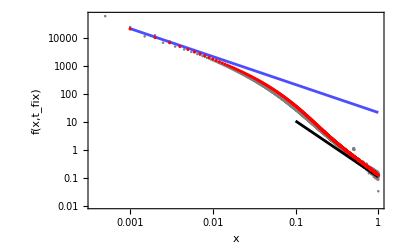

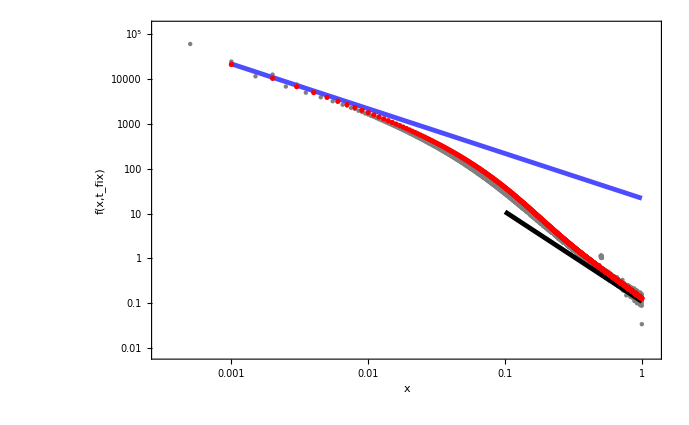

```mathematica
Quit[]
```

```mathematica
N1 = 1000;

sbar = 0.1 ;
x0 = 1/(2 N1);
h=0.5;
s[t_] :=(sbar);
sig=0.9;
F=sig/(2-sig);
N1=N1/(1+F);
sa=(h + (1-h) F);
sb=(1-(1-F) h);
k=1;
taui[t_] :=sa∫_0^t s[t1]ⅆt1;
pf1= ( 2/( NIntegrate[(E^(-taui[t])),{t,0,Infinity}]));
A= (sa-sb)/sb Log[sa/sb];
c1=pf1/(1-pf1);
ck=(1-(1-pf1)^k)/(1-pf1)^k;
C1=2 N1 pf1 ⅇ^-A ;
B[Te_]:= (2 N1)/NIntegrate[ⅇ^(sb/sa  taui[t]),{t,0,Te}];
Pnew[Te_]:=(sa 1 c1)/(sb ck)  (C1  B[Te]^2)/(2 N1) ⅇ^(sb/sa taui[Te]) NIntegrate[q^(-sa/sb) ⅇ^(-B[Te] q) ⅇ^(-C1 q^(-sa/sb))  Hypergeometric1F1[1-k,2,-C1 c1 q^(-sa/sb)],{q,0,Infinity},MaxRecursion->20];
NIntegrate[Te Pnew[Te],{Te,10,500},PrecisionGoal->15,WorkingPrecision->30,MaxRecursion->15]
```

NIntegrate::nlim: t = Te is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::inumr: The integrand (1. ⅇ^(-200./q^1.-(«6» q)/(«1»)))/q^1. has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::precw: The precision of the argument function ((220000. ⅇ^(0.0909091 Te) Te NIntegrate[«1»])/(NIntegrate[ⅇ^((«19» «1»)/(«19»)),{t,0,Te}]^2)) is less than WorkingPrecision (30.).

NIntegrate::inumr: The integrand (1. 2.718281828459045^(-(«36»)/q^(«21»)-(1100. q)/NIntegrate[«1»]))/q^1. has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 15 recursive bisections in Te near {Te} = {130.092435791166422210076300177}. NIntegrate obtained 121.637657657645749962320053855 and 3.85402395660375367447953369931×10^-11 for the integral and error estimates.

121.637657657645749962320053855

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

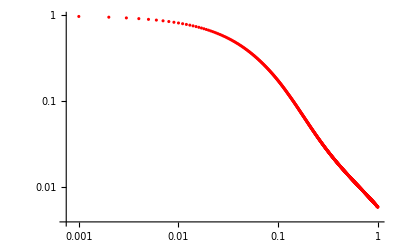

```mathematica
timePoints=Range[1,1000,1];

weightValues=Pnew/@timePoints;

(*Combine time points and their corresponding weights into a single list*)
Datatfix=Transpose[{timePoints,weightValues}];

f=sig/(2-sig);
N1= 1000/(1+f);
mu=10^-6;
L=10000;

theta=4 N1 mu L;
F=sig/(2-sig);
s=0.1;
h=0.5;
sa=s (h+ (1-h) F);
sb= s (1- (1-F) h);
x0=1/(2 2 sa N1);
x1=NDSolveValue[{D[x2a[t],t]==x2a[t]*(1-x2a[t]) (sa (1-x2a[t]) + sb x2a[t]),x2a[0]==x0},x2a,{t,0,1000}];

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,1000},{x,0,1}];
gData=Table[Sum[Datatfix[[k,2]] G[x,Datatfix[[k,1]]]/(x*(1-x)),{k,1,Length[Datatfix]}],{x,0.001,0.999,0.001}];

averageGData={};
AppendTo[averageGData,gData];
```

```mathematica
Quit[]
```

-Graphics-

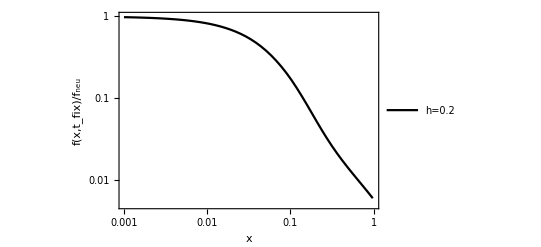

```mathematica
N1=1000;
mu=10^-6;
L=10000;
f=0.8181818181818181;
sa=(h + (1-h) f);
N1=N1/(1+f);
theta=4 N1 mu L; (* theta= 2 N mu *)
xaxis=Table[x,{x,0.001,0.999,0.001}];

Data=Transpose@{xaxis,xaxis gData/theta};
Data1=Interpolation@Data;

a4=ListLogLogPlot[Data,PlotStyle->Red];


Data1s=Data;

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];
interpolation=Interpolation[combinedData];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.5"},PlotRange->{{0.001,1},{0.003,1}}, PlotMarkers->{"■",12}];

a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Black},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.005,1}}];

(*Show both plots*)
Show[a1sInterpolated]
```

```mathematica
(.7)/(2-.7)
```

0.538462

```mathematica
Quit[]
```

```mathematica
N1 = 1000;

sbar = 0.1 ;
x0 = 1/(2 N1);
h=0.5;
s[t_] :=(sbar);
sig=0.7;
F=sig/(2-sig);
N1=N1/(1+F);
sa=(h + (1-h) F);
sb=(1-(1-F) h);
k=1;
taui[t_] :=sa∫_0^t s[t1]ⅆt1;
pf1= ( 2/( NIntegrate[(E^(-taui[t])),{t,0,Infinity}]));
A= (sa-sb)/sb Log[sa/sb];
c1=pf1/(1-pf1);
ck=(1-(1-pf1)^k)/(1-pf1)^k;
C1=2 N1 pf1 ⅇ^-A ;
B[Te_]:= (2 N1)/NIntegrate[ⅇ^(sb/sa  taui[t]),{t,0,Te}];
Pnew[Te_]:=(sa 1 c1)/(sb ck)  (C1  B[Te]^2)/(2 N1) ⅇ^(sb/sa taui[Te]) NIntegrate[q^(-sa/sb) ⅇ^(-B[Te] q) ⅇ^(-C1 q^(-sa/sb))  Hypergeometric1F1[1-k,2,-C1 c1 q^(-sa/sb)],{q,0,Infinity},MaxRecursion->20];
NIntegrate[Te Pnew[Te],{Te,10,500},PrecisionGoal->15,WorkingPrecision->30,MaxRecursion->15]
```

NIntegrate::nlim: t = Te is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::inumr: The integrand (1. ⅇ^(-200./q^1.-(1300. q)/(«1»)))/q^1. has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::precw: The precision of the argument function ((«1»)/(NIntegrate[ⅇ^((«19» «1»)/(«19»)),{t,0,Te}]^2)) is less than WorkingPrecision (30.).

NIntegrate::inumr: The integrand (1. 2.718281828459045^(-(«36»)/q^(«21»)-(1300. q)/NIntegrate[«1»,«1»]))/q^1. has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 15 recursive bisections in Te near {Te} = {153.734098388822672210076300177}. NIntegrate obtained 143.753595407684021342820225691 and 1.03098504224619638302111872995×10^-11 for the integral and error estimates.

143.753595407684021342820225691

```mathematica
timePoints=Range[1,1000,1];

weightValues=Pnew/@timePoints;

(*Combine time points and their corresponding weights into a single list*)
Datatfix=Transpose[{timePoints,weightValues}];

f=sig/(2-sig);
N1= 1000/(1+f);
mu=10^-6;
L=10000;

theta=4 N1 mu L;
F=sig/(2-sig);
s=0.1;
h=0.5;
sa=s (h+ (1-h) F);
sb= s (1- (1-F) h);
x0=1/(2 2 sa N1);
x1=NDSolveValue[{D[x2a[t],t]==x2a[t]*(1-x2a[t]) (sa (1-x2a[t]) + sb x2a[t]),x2a[0]==x0},x2a,{t,0,1000}];

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,1000},{x,0,1}];
gData=Table[Sum[Datatfix[[k,2]] G[x,Datatfix[[k,1]]]/(x*(1-x)),{k,1,Length[Datatfix]}],{x,0.001,0.999,0.001}];

averageGData={};
AppendTo[averageGData,gData];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

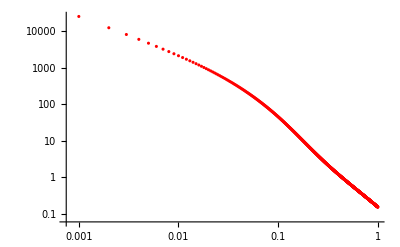

```mathematica
xaxis=Table[x,{x,0.001,0.999,0.001}];

Data=Transpose@{xaxis,gData};
Data1=Interpolation@Data;

a4=ListLogLogPlot[Data,PlotStyle->Red]
```

```mathematica
f
```

0.538462

```mathematica
Quit[]
```

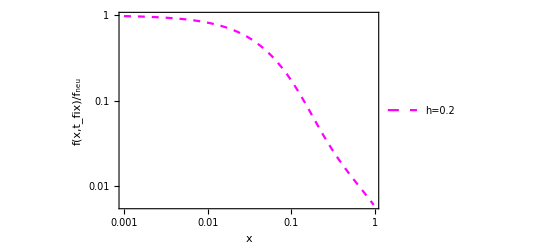

```mathematica
(*N1=1000;
mu=10^-6;
L=10000;
f=sig/(2-sig);
sa=(h + (1-h) f);
N1=N1/(1+f);*)
theta=4 N1 mu L; (* theta= 2 N mu *)
xaxis=Table[x,{x,0.001,0.999,0.001}];

Data=Transpose@{xaxis,xaxis gData/theta};
Data1=Interpolation@Data;

a4=ListLogLogPlot[Data,PlotStyle->Red];


Data1s=Data;

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];
interpolation=Interpolation[combinedData];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.5"},PlotRange->{{0.001,1},{0.003,1}}, PlotMarkers->{"■",12}];

a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Magenta,Dashed},PlotLegends->{"h=0.2"},PlotRange->All];

(*Show both plots*)
Show[a1sInterpolated]
```

```mathematica
sig=75
```

```mathematica
(.75)/(2-.75)
```

0.6

```mathematica
Quit[]
```

InputStream[…]

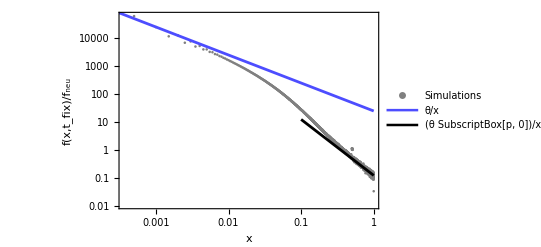

```mathematica
N1=1000;
mu=10^-6;
L=10000;
f=0.6;
sa=(h + (1-h) f);
N1=N1/(1+f);
theta=4 N1 mu L; (* theta= 2 N mu *)
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/Inbreeeding_recombination/average_data_check_f.txt"]
datas1s=ReadList[s1s,{Number,Number}];

Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];


Data1s=Transpose@{x11s,  x21s};

a1s=ListLogLogPlot[{Data1s}, Frame->True, FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003], FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Gray,Red,Magenta,Brown},PlotLegends->{"Simulations", "Diffusion"}];


a2s=LogLogPlot[ theta/( x),{x,10^-4,1},PlotStyle->{Lighter[Blue,0.3],Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\), \(x\)]\)",Medium]}];

a3s=LogLogPlot[theta/(2 1000 2 0.5 0.1 x^2),{x,0.1,1},PlotStyle->{Black,Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\\\ 
   \*SubscriptBox[\(p\), \(0\)]\), SuperscriptBox[\(x\), \(2\)]]\)",Medium]}];

Show[a1s,a2s,a3s]
```